## Model

### Variables

```mathematica
(*B0 to be determined with regression.*)
R =  0.02; (*Tube radius (m).*)
z0 = 0.035; (*Drop height from solenoid (m).*)
g = 9.8; (*Gravitational acceleration (m/s^2)*)
NT = 397; (*Number of wire turns.*)
Clear[B0]
```

### Models

```mathematica
AccelMotion[t_] := z0 - g t^2/2;
Solve[AccelMotion[t] == 0, t]
Field[z_] := B0 R^3/(R^2+z^2)^(3/2);

AccelField[t_] := Composition[Field, AccelMotion][t]
AccelVoltage[t_] := -NT Pi R^2 AccelField'[t]
```

{{t→-0.0845154},{t→0.0845154}}

### Minima

```mathematica
Clear[B0]
(*Finding minimum after time t = 0 of AccelFlux.*)
minimumVoltageModel = t/.Solve[AccelVoltage'[t] == 0, t, Reals][[3]];
(*Shifting AccelFlux minimum to t = 0.*)
AccelVoltageShifted[t_] := AccelVoltage[t + minimumVoltageModel];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

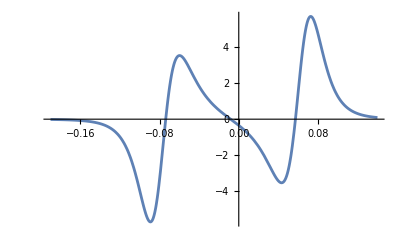

```mathematica
Clear[B0]
B0 = 0.34;
z0 = 0.021;
Plot[AccelVoltage[t], {t, 0, 1}];
Plot[AccelVoltageShifted[t], {t, -0.19, 0.14}, PlotRange->All]
```

```mathematica
3
```

```mathematica
100000
```

100000

## Data

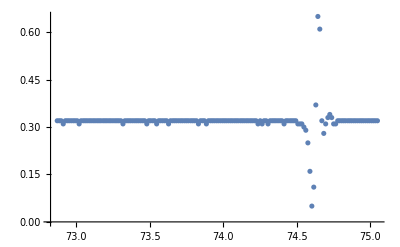

10.3125

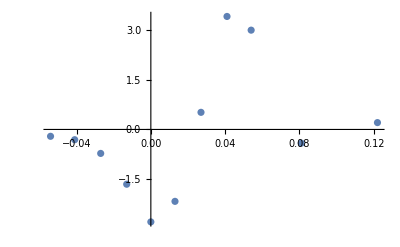

```mathematica
notePath = NotebookDirectory[];
fileName = "inputData\\big_magnet\\397_G_NO_REKT_5.txt";
fullName = StringJoin[{notePath, "\\", fileName}];
data = Import[fullName, "Data"][[2;;-2]];
ListPlot[data]
heightShift = 3.3 / 0.32
data = MapAt[heightShift# - 3.3&, data, {All,2}];

(*We'll shift the data so as to have the first minimum at t = 0.*)
positionOfMinimum = Position[data[[All, 2]], Min[data[[All, 2]]]][[1, 1]];
timeOfMinimum = data[[positionOfMinimum, 1]];

data = MapAt[# - timeOfMinimum &, data, {All, 1}];
noise = 0.00710383;
(*We filter the data points whose voltage is outside an interval away from zero.*)
data = Select[data,Abs[#[[2]]] > 0.15 &];
dataPlot = ListPlot[data, PlotRange->All]
```

## Fitting

FindFit::fitm: フィットパラメータについて解くことができませんでした．デザイン行列は非矩形または非数値的であるか，あるいは逆行列が存在しません．

General::ivar: -0.0999959は有効な変数ではありません．

General::ivar: -0.0959143は有効な変数ではありません．

General::ivar: -0.0918326は有効な変数ではありません．

General::stop: この計算中に，General::ivarのこれ以上の出力は表示されません．

FindFit::fitm: フィットパラメータについて解くことができませんでした．デザイン行列は非矩形または非数値的であるか，あるいは逆行列が存在しません．

ReplaceAll::reps: {NonlinearModelFit[{{-0.054,-0.20625},{-0.041,-0.309375},{-0.027,-0.721875},{-0.013,-1.65},{0.,-2.78438},{0.013,-2.16563},{0.027,0.515625},{0.041,3.40313},{0.054,2.99062},{0.081,-0.4125},«1»},-(0.000117338 B0 («20»+t) (-4.9 («20»+t)^2+z0))/((0.0004+(«1»)^2)^(5/2)),B0,t][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::fitm: フィットパラメータについて解くことができませんでした．デザイン行列は非矩形または非数値的であるか，あるいは逆行列が存在しません．

ReplaceAll::reps: {NonlinearModelFit[{{-0.054,-0.20625},{-0.041,-0.309375},{-0.027,-0.721875},{-0.013,-1.65},{0.,-2.78438},{0.013,-2.16563},{0.027,0.515625},{0.041,3.40313},{0.054,2.99062},{0.081,-0.4125},«1»},-(0.000117338 B0 («20»+t) (-4.9 («20»+t)^2+z0))/((0.0004+(«1»)^2)^(5/2)),B0,t][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindFit::fitm: フィットパラメータについて解くことができませんでした．デザイン行列は非矩形または非数値的であるか，あるいは逆行列が存在しません．

NonlinearModelFit[{{-0.054,-0.20625},{-0.041,-0.309375},{-0.027,-0.721875},{-0.013,-1.65},{0.,-2.78438},{0.013,-2.16563},{0.027,0.515625},{0.041,3.40313},{0.054,2.99062},{0.081,-0.4125},{0.122,0.20625}},-(0.000117338 B0 (0.0729596+t) (-4.9 (0.0729596+t)^2+z0))/((0.0004+(-4.9 (0.0729596+t)^2+z0)^2)^(5/2)),B0,t][ParameterTable]

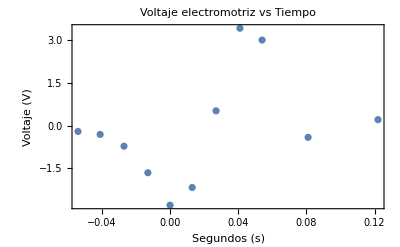

```mathematica
Clear[B0]
fitModel = NonlinearModelFit[data, AccelVoltageShifted[t], B0, t];fitPlot = Plot[fitModel[t], {t, -0.1, 0.1}, PlotStyle->Red, PlotRange->All];

accelPlot = Plot[AccelVoltageShifted[t], {t,-0.06, 0.06}, PlotStyle->Green , PlotRange->All];

B0Fitted = B0/.fitModel["BestFitParameters"];
parameterTable = fitModel["ParameterTable"]

Show[fitPlot, dataPlot, accelPlot, PlotLabel->"Voltaje electromotriz vs Tiempo", Frame->True, FrameLabel->{"Segundos (s)", "Voltaje (V)"}]
```